Exact Solutions of a Fokker-Planck Equation

MJ Englefield, J Stat Phys, Vol. 52 (1988)
Notebook: Óscar Amaro, January 2023 @ GoLP-EPP

Introduction
In this notebook we reproduce some results from the paper.

5. DISCUSSION AND CONCLUSION:
“This paper has given exact, explicit solutions involving only elementary functions for a Fokker-Planck equation with a potential of the form u = 2 h^2 log(ϕ(x))... In the potential there are four parameters that can be chosen to approximate any other required form, while the solutions contain parameters that can be chosen to simulate a required initial configuration”

## If ψ solves eq 2.4 then W solves eq 2.1

```mathematica
Clear[V,W,ψ,u,x,t,h,eq21]
W=ψ[x,t] Exp[(-u[x])/(2 h^2)];
(* eq 2.5 *)
V=1/(4 h^2)D[u[x],x]^2-0.5D[u[x],{x,2}];
(* eq 2.1 and replace dψdt by eq 2.4 *)
eq21=(h^2 D[W,{x,2}]+D[D[u[x],x] W,x]-D[W,t])//Simplify
eq21/.{Derivative[0,1][ψ][x,t]->h^2 Derivative[2,0][ψ][x,t]-V ψ[x,t]}//FullSimplify
```

(ⅇ^(-u[x]/(2 h^2)) (-ψ[x,t] (u'[x]^2-2 h^2 u''[x])-4 h^2 ψ^(0,1)[x,t]+4 h^4 ψ^(2,0)[x,t]))/(4 h^2)

0.

## eq 2.3 solves eq 2.1

```mathematica
Clear[x,t,w,u,h,LHS]
(* eq 2.3 time-independent function, h is constant, not a function of x *)
w=Exp[-u[x]/h^2];
(* eq 2.1 *)
LHS=h^2 D[w,{x,2}]+D[D[u[x],x] w,x]
LHS//Simplify
```

-(ⅇ^(-u[x]/h^2) u'[x]^2)/h^2+ⅇ^(-u[x]/h^2) u''[x]+h^2 ((ⅇ^(-u[x]/h^2) u'[x]^2)/h^4-(ⅇ^(-u[x]/h^2) u''[x])/h^2)

0

## eq 2.8 is solution to eq 2.4 if V=0 (heat equation)

```mathematica
(* if V(x)=0, a solution to 2.4 is *)
Clear[ψ,x,t,h,a,β,V]
(* eq 2.8 *)
ψ=(1+2β h^2 t)^(-1/2)Exp[-(β(x-a)^2)/(2(1+2β h^2 t))];
V=0;
(* eq 2.4 *)
h^2 D[ψ,{x,2}]-V ψ-D[ψ,t]//Simplify
```

0

```mathematica
(* cosh αx satisfies 2.6 with λ=-h^2 α^2 -> replace Exp[-u/2 h^2] with Cosh[α x]*)
Clear[t,x,a,β,h,ψ,W,u,eq21,f]
f=Cosh[α x];
λ=-h^2 α^2;
-h^2 D[f,{x,2}]-λ f
```

0

## eq 2.9 is solution to eq 2.1

```mathematica
Clear[t,x,a,β,h,ψ,W,u,eq21,α,ρ,k,ν]
(* definition before eq 2.15 *)
ρ=1/(1+2β h^2 t);
(* eq 2.15 *)
W=-k Sqrt[ρ]Sech[ν x](ν Tanh[ν x]+ρ β(x-a))Exp[-ν^2 h^2 t-β ρ(x-a)^2/2]+0.5 ν Sech[ν x]^2;
(* potential defined after eq 2.15*)
u=h^2 Log[Cosh[ν x]^2];
eq21=h^2 D[W,{x,2}]+D[D[u,x] W,x]-D[W,t]//FullSimplify
```

0

## eq 2.15 is solution to eq 2.1

```mathematica
Clear[t,x,a,β,h,ψ,W,u,eq21,α]
(* eq 2.8 *)
ψ=(1+2β h^2 t)^(-1/2)Exp[-(β(x-a)^2)/(2(1+2β h^2 t))];
(* eq 2.9 *)
W=ψ Cosh[α x] Exp[-h^2 α^2 t]//Simplify;
(* inverted potential defined after eq 2.9*)
u=h^2 Log[Sech[α x]^2];
eq21=h^2 D[W,{x,2}]+D[D[u,x] W,x]-D[W,t]//FullSimplify//Expand
```

0

## Figure 1 transient solutions

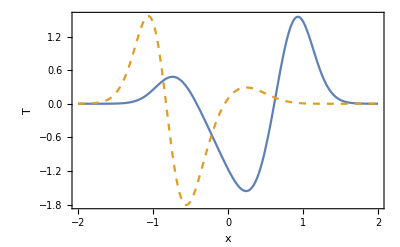

1.80411×10^-16

-1.05471×10^-15

```mathematica
Clear[T,β,a,x,t,ν,γ,ω,θ,ρ,ϕ]
(* definition before eq 2.15 *)
ρ=1/(1+2β h^2 t);
(* eq 3.5 *)
T=(-β ρ-ν^2+β^2 ρ^2(x-a)^2+((γ^2-ν^2)(β ρ (x-a)+ν Tanh[ν x+ω]))/(γ Coth[γ x+θ]-ν Tanh[ν x+ω]))(√ρ)/ϕ Exp[-γ^2 h^2 t-(β ρ(x-a)^2)/2];
ϕ=h γ Cosh[γ x+θ]-h ν Tanh[ν x+ω]Sinh[γ x+θ];
(* parameters *)
h=0.35355;ν=2.59;γ=2.67;ω=0.285;θ=-0.63;

Plot[{h^2 T/.{β->6.4,a->0.106,t->0},h^2 T/.{β->8,a->-0.53,t->0}},{x,-2,+2},Frame->True,FrameLabel->{"x","T"},PlotStyle->{Default,Dashed}]

(* integral = 0 on (-∞,+∞) *)
NIntegrate[T/.{β->6.4,a->0.106,t->0},{x,-∞,+∞}]//Quiet
NIntegrate[T/.{β->8,a->-0.53,t->0},{x,-∞,+∞}]//Quiet
```

## Figure 2

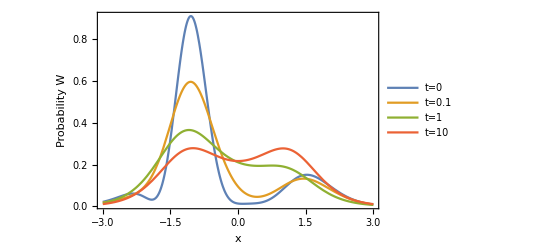

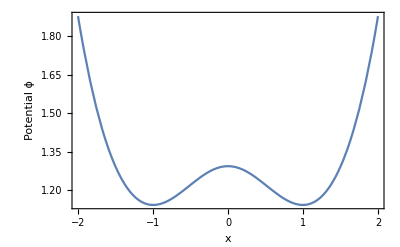

```mathematica
Clear[T,β,a,x,t,ν,γ,ω,θ,ρ,k1,k2,a1,a2,f,ϕ,c,β1,β2,W,μ,h,g]
(* definition before eq 2.15 *)
ρ=1/(1+2β h^2 t);
μ=-h^2 γ^2;

(* eq 3.1 *)
ϕ=h γ Cosh[γ x+θ]-h ν Tanh[ν x+ω]Sinh[γ x+θ];

(* eq 3.3 *)
g=(h^2 γ(γ^2-ν^2))/(2 ϕ^2);

(* eq 3.4 ??? *)
f=Sinh[γ x+θ](Exp[(ν^2-γ^2)h^2 t])/(ϕ^2 Cosh[ν x+ω]);

(* eq 3.5 *)
T=(-β ρ-ν^2+β^2 ρ^2(x-a)^2+((γ^2-ν^2)(β ρ (x-a)+ν Tanh[ν x+ω]))/(γ Coth[γ x+θ]-ν Tanh[ν x+ω]))(√ρ)/ϕ Exp[-γ^2 h^2 t-(β ρ(x-a)^2)/2];

(* eq 3.6 *)
W=g + c f+k1 (T/.{β->β1,a->a1})+k2( T/.{β->β2,a->a2});

c=-0.177;
β1=4.7;
a1=-1.1;
k1=-0.095;
β2=1;
a2=0.5;
k2=0.09;

h=1;
γ=1.293;
ν=1.054;
θ=ω=0;

Plot[{W/.{t->0},W/.{t->0.1},W/.{t->1},W/.{t->10}},{x,-3,+3},Frame->True,FrameLabel->{"x","Probability W"},PlotRange->All,PlotLegends->{"t=0","t=0.1","t=1","t=10"}]

Plot[ϕ,{x,-2,+2},Frame->True,FrameLabel->{"x","Potential ϕ"}]
```

## Figure 3

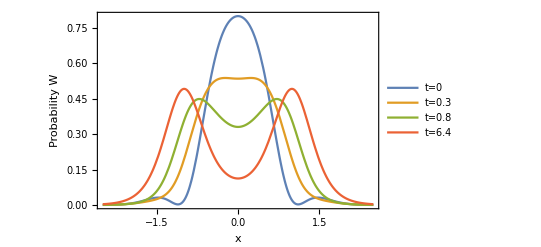

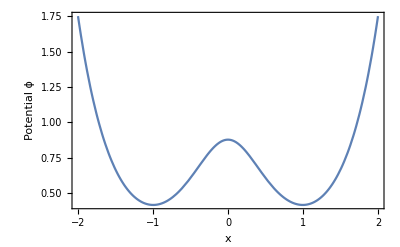

```mathematica
Clear[T,β,a,x,t,ν,γ,ω,θ,ρ,k1,k2,a1,a2,f,ϕ,c,β1,β2,W,μ,h,g]
(* definition before eq 2.15 *)
ρ=1/(1+2β h^2 t);
μ=-h^2 γ^2;

(* eq 3.1 *)
ϕ=h γ Cosh[γ x+θ]-h ν Tanh[ν x+ω]Sinh[γ x+θ];

(* eq 3.3 *)
g=(h^2 γ(γ^2-ν^2))/(2 ϕ^2);

(* eq 3.4 ??? *)
f=Sinh[γ x+θ](Exp[(ν^2-γ^2)h^2 t])/(ϕ^2 Cosh[ν x+ω]);

(* eq 3.5 *)
T=(-β ρ-ν^2+β^2 ρ^2(x-a)^2+((γ^2-ν^2)(β ρ (x-a)+ν Tanh[ν x+ω]))/(γ Coth[γ x+θ]-ν Tanh[ν x+ω]))(√ρ)/ϕ Exp[-γ^2 h^2 t-(β ρ(x-a)^2)/2];

(* eq 3.6 *)
W=g + c f+k1 (T/.{β->β1,a->a1})+k2( T/.{β->β2,a->a2});

c=0;
β1=3.6;
a1=0;
k1=-0.06833;
β2=0.9;
a2=0;
k2=-0.014833;

h=0.4082;
γ=2.152;
ν=2.038;
θ=ω=0;

Plot[{W/.{t->0},W/.{t->0.3},W/.{t->0.8},W/.{t->6.4}},{x,-2.5,+2.5},Frame->True,FrameLabel->{"x","Probability W"},PlotRange->All,PlotLegends->{"t=0","t=0.3","t=0.8","t=6.4"}]

Plot[ϕ,{x,-2,+2},Frame->True,FrameLabel->{"x","Potential ϕ"}]
```

## Figure 4

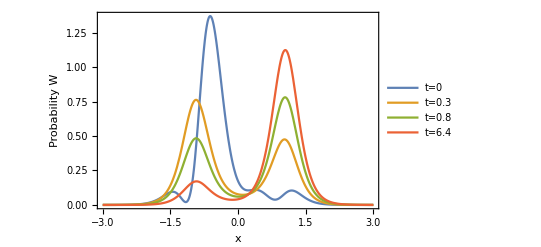

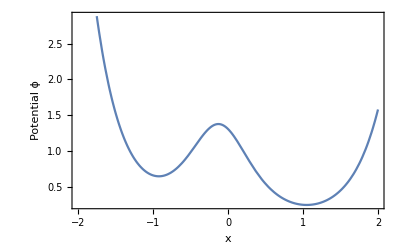

```mathematica
Clear[T,β,a,x,t,ν,γ,ω,θ,ρ,k1,k2,a1,a2,f,ϕ,c,β1,β2,W,μ,h,g]
(* definition before eq 2.15 *)
ρ=1/(1+2β h^2 t);
μ=-h^2 γ^2;

(* eq 3.1 *)
ϕ=h γ Cosh[γ x+θ]-h ν Tanh[ν x+ω]Sinh[γ x+θ];

(* eq 3.3 *)
g=(h^2 γ(γ^2-ν^2))/(2 ϕ^2);

(* eq 3.4 ??? *)
f=Sinh[γ x+θ](Exp[(ν^2-γ^2)h^2 t])/(ϕ^2 Cosh[ν x+ω]);

(* eq 3.5 *)
T=(-β ρ-ν^2+β^2 ρ^2(x-a)^2+((γ^2-ν^2)(β ρ (x-a)+ν Tanh[ν x+ω]))/(γ Coth[γ x+θ]-ν Tanh[ν x+ω]))(√ρ)/ϕ Exp[-γ^2 h^2 t-(β ρ(x-a)^2)/2];

(* eq 3.6 *)
W=g + c f+k1 (T/.{β->β1,a->a1})+k2( T/.{β->β2,a->a2});

c=-0.13;
β1=6.4;
a1=0.106;
k1=-0.01375;
β2=8.0;
a2=-0.53;
k2=-0.0625;

h=0.35355;
γ=2.67;
ν=2.59;
θ=-0.63;
ω=0.285;

Plot[{W/.{t->0},W/.{t->6},W/.{t->18},W/.{t->100}},{x,-3,+3},Frame->True,FrameLabel->{"x","Probability W"},PlotRange->All,PlotLegends->{"t=0","t=0.3","t=0.8","t=6.4"}]

Plot[ϕ,{x,-2,+2},Frame->True,FrameLabel->{"x","Potential ϕ"}]
```